```mathematica
SetDirectory[NotebookDirectory[]];
pblue=RGBColor[1,0,0,0.65];
pyellow=RGBColor[1,1,0,0.65];
pred=RGBColor[173/255,216/255,230/255,0.65];
pgreen=RGBColor[1,0,1,0.65];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
phase[args:{_?NumericQ..}]:=Module[{},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]];
```

{2,9500.,0.1}

{{runtime:,2.084744},{2,0.950000,1.000000,1,0.618544,3.162442}}

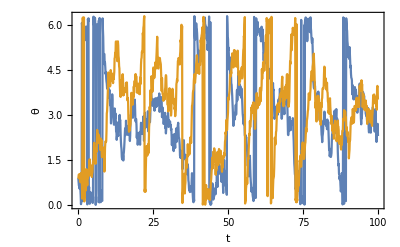

0.618537

```mathematica
filebase="data/test";
strlst=ReadList[filebase<>".out",String];
{n, t1, dt}=ToExpression[StringSplit[strlst[[1]]][[1;;3]]]
StringSplit[strlst[[-2;;-1]]]
AbsoluteTiming[dat=Partition[BinaryReadList[filebase<>".dat","Real64"],n]];
Nt=Length[dat];
data=Transpose[dat[[1;;Length[dat]]],{2,1}];
ListPlot[(Transpose[{Range[Nt]*dt,#}]&/@Mod[data,2*Pi])[[All,1;;1000]],Joined->True,Axes->False,Frame->True,FrameLabel->{t,θ},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->All,RotateLabel->False]
Mean[Abs[Total[Exp[I*data[[All,All]]]]/2]^2]
```

{2,9500.,0.01}

{{runtime:,172.355612},{2,0.950000,1.000000,1,0.621765,9.995013}}

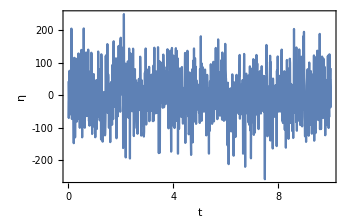

```mathematica
filebase="data/knoise1";
strlst=ReadList[filebase<>".out",String];
{n, t1, dt}=ToExpression[StringSplit[strlst[[1]]][[1;;3]]]
StringSplit[strlst[[-2;;-1]]]
noise=Transpose[Partition[BinaryReadList[filebase<>"noise.dat","Real64"],n],{2,1}];
ListPlot[{Transpose[{Range[Length[noise[[1]]]]*dt,noise[[1]]}[[All,1;;1000]]]},Joined->True,Axes->False,Frame->True,FrameLabel->{t,η},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->All,ImageSize->350,FrameTicks->{{Table[i,{i,-200,200,100}],Table[{i,""},{i,-200,200,100}]},{Table[i,{i,0,10,2}],Table[{i,""},{i,0,10,2}]}},ImagePadding->{{65,15},{65,15}}]
```

```mathematica
Length[diffs1]
Length[diffs2]
test1=Transpose[{Range[Length[diffs1]]*dt,diffs1}[[All,1;;10000;;10]]];
test2=Transpose[{Range[Length[diffs2]]*dt,diffs2}[[All,1;;10000;;10]]];
```

950001

950001

{2,9500.,0.01}

{{runtime:,146.867873},{2,0.950000,1.000000,1,0.499918,10.005159}}

{2,9500.,0.01}

{{runtime:,172.355612},{2,0.950000,1.000000,1,0.621765,9.995013}}

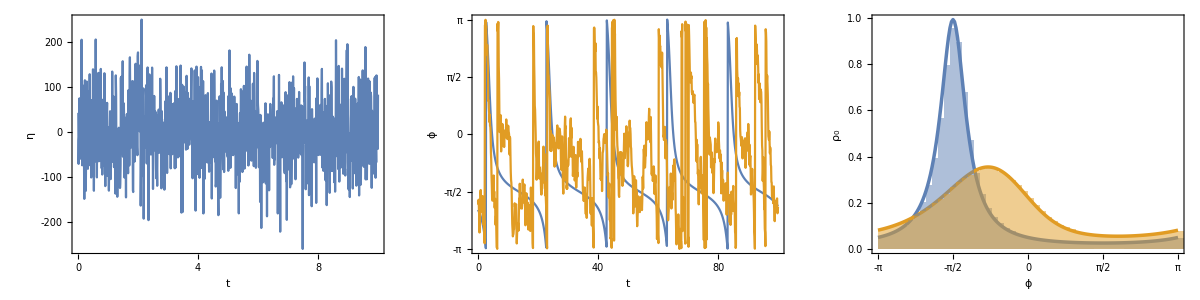

kuramotoplots.pdf

```mathematica
filebase="data/knoise0";
strlst=ReadList[filebase<>".out",String];
{n, t1, dt}=ToExpression[StringSplit[strlst[[1]]][[1;;3]]]
StringSplit[strlst[[-2;;-1]]]
data=Transpose[Partition[BinaryReadList[filebase<>".dat","Real64"],n],{2,1}];
diffs1=Mod[-First@Differences[data]+Pi,2*Pi]-Pi;
filebase="data/knoise1";
strlst=ReadList[filebase<>".out",String];
{n, t1, dt}=ToExpression[StringSplit[strlst[[1]]][[1;;3]]]
StringSplit[strlst[[-2;;-1]]]
data=Transpose[Partition[BinaryReadList[filebase<>".dat","Real64"],n],{2,1}];
diffs2=Mod[-First@Differences[data]+Pi,2*Pi]-Pi;
noise=Transpose[Partition[BinaryReadList[filebase<>"noise.dat","Real64"],n],{2,1}];


c=0;
nbins=50;
fplst1=Partition[Partition[Flatten[Import["data/fplst1.dat"]],2],201];
vals1=nbins/(2*Pi)*N[BinCounts[diffs1,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs1])];
rects1=Table[Rectangle[{-Pi+2*Pi/nbins*(i-1)-c*Pi/nbins,0},{-Pi+2*Pi/nbins*(i-1)+(2-c)*Pi/nbins,vals1[[i]]}],{i,1,Length[vals1]}];
vals2=nbins/(2*Pi)*N[BinCounts[diffs2,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs2])];
rects2=Table[Rectangle[{-Pi+2*Pi/nbins*(i-1)-c*Pi/nbins,0},{-Pi+2*Pi/nbins*(i-1)+(2-c)*Pi/nbins,vals2[[i]]}],{i,1,Length[vals2]}];
p0=ListPlot[{Transpose[{Range[Length[noise[[1]]]]*dt,noise[[1]]}[[All,1;;1000]]]},Joined->True,Axes->False,Frame->True,FrameLabel->{t,η},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->All,ImageSize->350,FrameTicks->{{Table[i,{i,-200,200,100}],Table[{i,""},{i,-200,200,100}]},{Table[i,{i,0,10,2}],Table[{i,""},{i,0,10,2}]}},ImagePadding->{{65,15},{65,15}}];
p1=ListPlot[{Transpose[{Range[Length[diffs1]]*dt,diffs1}[[All,1;;10000;;10]]],Transpose[{Range[Length[diffs2]]*dt,diffs2}[[All,1;;10000;;10]]]},Joined->True,Axes->False,Frame->True,FrameLabel->{t,ϕ},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->All,ImageSize->350,FrameTicks->{{{{-π,-π},{-π/2,DisplayForm[RowBox[{-Pi,"/",2}]]},{0,0},{π/2,DisplayForm[RowBox[{Pi,"/",2}]]},{π,π}},{{-π,""},{-π/2,""},{0,""},{π/2,""},{π,""}}},{Table[i,{i,0,100,20}],Table[{i,""},{i,0,100,20}]}},ImagePadding->{{65,15},{65,15}}];
p2=ListPlot[{fplst1[[1]],fplst1[[6]]},Joined->True,Axes->False,Frame->True,FrameLabel->{{Subscript[ρ,0],None},{ϕ,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]},{{{-π,-π},{-π/2,DisplayForm[RowBox[{-Pi,"/",2}]]},{0,0},{π/2,DisplayForm[RowBox[{Pi,"/",2}]]},{π,π}},{{-π,""},{-π/2,""},{0,""},{π/2,""},{π,""}}}},PlotStyle->Directive[AbsoluteThickness[2.5]],Epilog->{Opacity[0.5],ColorData[97,"ColorList"][[1]],rects1,ColorData[97,"ColorList"][[2]],rects2},ImageSize->350,ImagePadding->{{65,15},{65,15}}];
p=Grid[{{p0,p1,p2}}]
Export["kuramotoplots.pdf",p]
```

```mathematica
ListPlot[{Transpose[{Range[Length[noise[[1]]]]*dt,noise[[1]]}[[All,1;;100]]]},Joined->True,Axes->False,Frame->True,FrameLabel->{t,η},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->All,ImageSize->350,FrameTicks->{{Table[i,{i,-200,200,100}],Table[{i,""},{i,-200,200,100}]},{Table[i,{i,0,100,20}],Table[{i,""},{i,0,100,20}]}},ImagePadding->{{65,15},{65,15}}]
```

-Graphics-

```mathematica
Total[Cos[#[[1]]/2]^2*#[[2]]&/@fplst1[[1]]]/Total[#[[2]]&/@fplst1[[1]]]
Total[Cos[#[[1]]/2]^2*#[[2]]&/@fplst1[[6]]]/Total[#[[2]]&/@fplst1[[6]]]
```

0.499221

0.621761

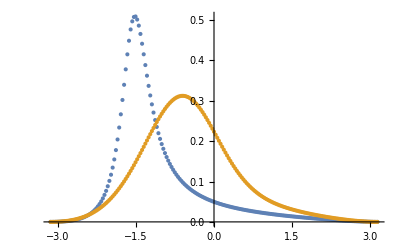

```mathematica
ListPlot[{{#[[1]],Cos[#[[1]]/2]^2*#[[2]]}&/@fplst1[[1]],{#[[1]],Cos[#[[1]]/2]^2*#[[2]]}&/@fplst1[[6]]}]
```

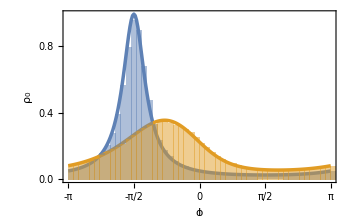

```mathematica
ListPlot[{fplst1[[1]],fplst1[[6]]},Joined->True,Axes->False,Frame->True,FrameLabel->{{Subscript[ρ,0],None},{ϕ,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]},{{{-π,-π},{-π/2,DisplayForm[RowBox[{-Pi,"/",2}]]},{0,0},{π/2,DisplayForm[RowBox[{Pi,"/",2}]]},{π,π}},{{-π,""},{-π/2,""},{0,""},{π/2,""},{π,""}}}},PlotStyle->Directive[AbsoluteThickness[2.5]],Epilog->{Opacity[0.5],ColorData[97,"ColorList"][[1]],rects1,ColorData[97,"ColorList"][[2]],rects2},ImageSize->350,ImagePadding->{{65,15},{65,15}}]
```

```mathematica
R[ϵ_,δω_,δ_]:=1/2+1/2*(NIntegrate[Cos[η]*Exp[(δω*(z-η)-ϵ*(Cos[z]-Cos[η]))/δ],{η,0,2*Pi},{z,0,η}]+(Exp[-2*Pi*δω/δ]/(1-Exp[-2*Pi*δω/δ])*NIntegrate[Cos[η]*Exp[(δω*(z-η)-ϵ*(Cos[z]-Cos[η]))/δ],{η,0,2*Pi},{z,0,2*Pi}]))/(NIntegrate[Exp[(δω*(z-ψ)-ϵ*(Cos[z]-Cos[ψ]))/δ],{ψ,0,2*Pi},{z,0,ψ}]+(Exp[-2*Pi*δω/δ]/(1-Exp[-2*Pi*δω/δ])*NIntegrate[Exp[(δω*(z-ψ)-ϵ*(Cos[z]-Cos[ψ]))/δ],{ψ,0,2*Pi},{z,0,2*Pi}]));
dη=Pi/100;
dϵ=0.01;
ρ[ϵ_,δω_,δ_,η_]:=(NIntegrate[Exp[(δω*(z-η)-ϵ*(Cos[z]-Cos[η]))/δ],{z,0,η}]+(Exp[-2*Pi*δω/δ]/(1-Exp[-2*Pi*δω/δ])*NIntegrate[Exp[(δω*(z-η)-ϵ*(Cos[z]-Cos[η]))/δ],{z,0,2*Pi}]))/(NIntegrate[Exp[(δω*(z-ψ)-ϵ*(Cos[z]-Cos[ψ]))/δ],{ψ,0,2*Pi},{z,0,ψ}]+(Exp[-2*Pi*δω/δ]/(1-Exp[-2*Pi*δω/δ])*NIntegrate[Exp[(δω*(z-ψ)-ϵ*(Cos[z]-Cos[ψ]))/δ],{ψ,0,2*Pi},{z,0,2*Pi}]))
AbsoluteTiming[Monitor[fplst1=Join[{Table[{η,1/(1.0+0.95*Sin[η])/((2*π)/(√(1-0.95^2)))},{η,-Pi,Pi,dη}]},Table[{η,ρ[0.95,1.0,δ^2/2,Mod[η,2*Pi]]},{δ,0.2,2.0,0.2},{η,-Pi,Pi,dη}]];,{δ,η/(2.0*Pi)}]]
AbsoluteTiming[Monitor[fplst2=Join[{Table[{ϵ,Piecewise[{{1/2,Abs[ϵ]<1},{1/2+1/2*(1-1/ϵ^2)^(1/2), ϵ>=1},{1/2-1/2*(1-1/ϵ^2)^(1/2), ϵ<=-1}}]},{ϵ,0,2,dϵ}]},Table[{ϵ,R[ϵ,1.0,δ^2/2]},{δ,0.2,2.0,0.2},{ϵ,0,2,dϵ}]];,{δ,ϵ}]]
AbsoluteTiming[Monitor[fplst3=Join[{{0,0.5}},Table[{σ,R[0.95,1.0,σ^2/2]},{σ,0.05,5.0,0.05}]];,σ]]
Export["data/fplst1.dat",Flatten[N[fplst1]]]
Export["data/fplst2.dat",Flatten[N[fplst2]]]
Export["data/fplst3.dat",Flatten[N[fplst3]]]
```

```mathematica
fplst1=Partition[Partition[Flatten[Import["data/fplst1.dat"]],2],201];
fplst2=Partition[Partition[Flatten[Import["data/fplst2.dat"]],2],201];
fplst3=Partition[Flatten[Import["data/fplst3.dat"]],2];
fplst4=Join[{{0,0.5}},Table[{σ,0.5},{σ,0.05,5.0,0.05}]];
```

/Users/zack/Documents/oscillators/uncorrelated

{{0.,0.500018},{0.5,0.587053},{1.,0.623795},{1.5,0.619239},{2.,0.593318},{2.5,0.566196},{3.,0.548698},{3.5,0.537794},{4.,0.529093},{4.5,0.523239},{5.,0.518684}}

{{0.,0.500018},{0.5,0.500018},{1.,0.500018},{1.5,0.500018},{2.,0.500018},{2.5,0.500018},{3.,0.500018},{3.5,0.500018},{4.,0.500018},{4.5,0.500018},{5.,0.500018}}

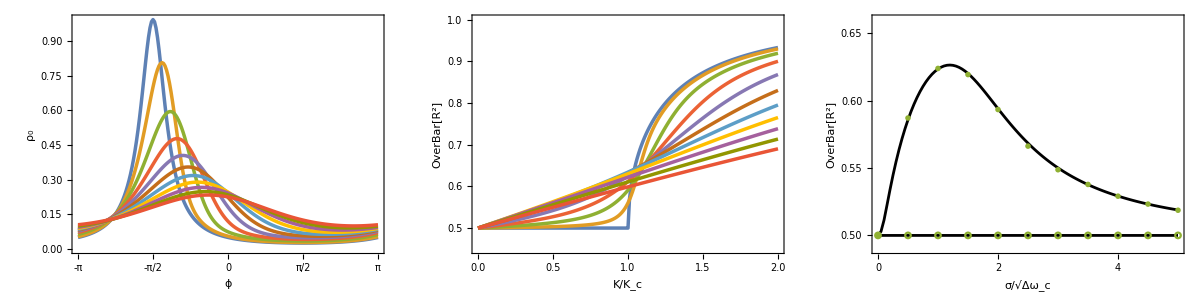

plots/fig2.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
dη=Pi/100;
dϵ=0.01;
uncorrelatedaddconst=Table[ToExpression[StringSplit[ReadList["data/knoise/uncorrelatedaddconst"<>ToString[i]<>".out",String]]][[1,{3,5}]],{i,0,10}]
correlatedaddconst=Table[ToExpression[StringSplit[ReadList["data/knoise/correlatedaddconst"<>ToString[i]<>".out",String]]][[1,{3,5}]],{i,0,10}]
imgSize={350,350};
imgPadding={{75,50},{75,50}};
p1=ListPlot[fplst1,Joined->True,Axes->False,Frame->True,FrameLabel->{{Subscript[ρ,0],None},{ϕ,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,FrameTicks->{{Automatic,None},{Table[x,{x,-Pi,Pi,Pi/2}],None}},ImageSize->imgSize,ImagePadding->imgPadding,AspectRatio->1/2,PlotStyle->Directive[AbsoluteThickness[2.5]]];
p2=ListPlot[fplst2,Joined->True,Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{K,"/",Subscript[K,c]}]],OverBar[R^2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{0.45,1},ImageSize->imgSize,ImagePadding->imgPadding,FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0.5,1,0.1}],None},{Table[{i,PaddedForm[i,{2,1}]},{i,0,2,0.5}],None}},AspectRatio->1/2,PlotStyle->Directive[AbsoluteThickness[2.5]]];
fplst4=Table[{ϵ,0.5},{ϵ,0,5,dϵ}];
p31=ListPlot[{fplst3,fplst4},Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{σ,"/",Subscript[Δω,c]^(1/2)}]],OverBar[R^2]},LabelStyle->Directive[16],PlotRange->{0.49,0.66},Joined->True,PlotStyle->{Directive[Black,AbsoluteThickness[2]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0.5,0.7,0.05}],None},{Table[i,{i,0,5}],None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->imgSize,ImagePadding->imgPadding,AspectRatio->1/2];
p32=ListPlot[{uncorrelatedaddconst,correlatedaddconst},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[3]],Thick,Disk[]}],0.1},{Graphics[{ColorData[97,"ColorList"][[3]],Thick,Circle[]}],0.1}}];
p3=Show[p31,p32];
p=Grid[{{p1,p2,p3}}]
Export["plots/fig2.pdf",p]
```

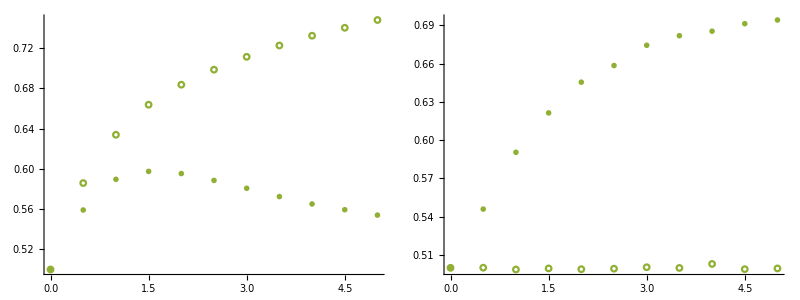

```mathematica
correlatedaddtrig=Table[ToExpression[StringSplit[ReadList["data/knoise/correlatedaddtrig"<>ToString[i]<>".out",String][[-1]]]][[{3,5}]],{i,0,10}];
uncorrelatedaddtrig=Table[ToExpression[StringSplit[ReadList["data/knoise/uncorrelatedaddtrig"<>ToString[i]<>".out",String][[-1]]]][[{3,5}]],{i,0,10}];
correlatedmult=Table[ToExpression[StringSplit[ReadList["data/knoise/correlatedmult"<>ToString[i]<>".out",String][[-1]]]][[{3,5}]],{i,0,10}];
uncorrelatedmult=Table[ToExpression[StringSplit[ReadList["data/knoise/uncorrelatedmult"<>ToString[i]<>".out",String][[-1]]]][[{3,5}]],{i,0,10}];
Grid[{{ListPlot[{uncorrelatedaddtrig,correlatedaddtrig},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[3]],Thick,Disk[]}],0.05},{Graphics[{ColorData[97,"ColorList"][[3]],Thick,Circle[]}],0.05}},ImageSize->350],
ListPlot[{uncorrelatedmult,correlatedmult},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[3]],Thick,Disk[]}],0.05},{Graphics[{ColorData[97,"ColorList"][[3]],Thick,Circle[]}],0.05}},ImageSize->350]}}]
```

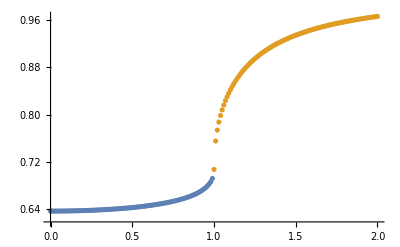

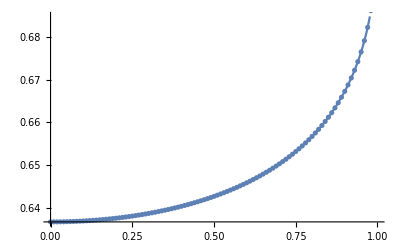

```mathematica
dk=0.01;
ListPlot[{Table[{k,NIntegrate[Abs[Cos[η/2]]/(1+k*Sin[η])/((2*π)/(√(1-k^2))),{η,0,2*Pi}]},{k,0,1.0-dk,dk}],Table[{k,((√((k+√(-1+k^2))/k))/(√2))},{k,1,2,dk}]}]
Show[Plot[(ⅈ (-√(k+ⅈ √(1-k^2)) ArcTanh[√2 √(k (k+ⅈ √(1-k^2)))]+√(k-ⅈ √(1-k^2)) ArcTanh[(√2)/(√(1+(ⅈ √(1-k^2))/k))]))/(√2 √k π),{k,0,1}],ListPlot[{Table[{k,NIntegrate[Abs[Cos[η/2]]/(1+k*Sin[η])/((2*π)/(√(1-k^2))),{η,0,2*Pi}]},{k,0,1.0-dk,dk}]}]]
```